## Plotting L=12 TFD Spread Complexity

```mathematica
tList1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KCW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KIPRW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KEntW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0 = Exp[#] &/@ KEntW0;
```

```mathematica
KCpltW0=ListLinePlot[Transpose[{tList1,KCW0}],PlotRange->All];
```

```mathematica
tList2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KCW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt01 = Exp[#] &/@ KEntW0pt01;
```

```mathematica
KCpltW0pt01=ListLinePlot[Transpose[{tList1,KCW0pt01}],PlotRange->All];
```

```mathematica
tList3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KCW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt1 = Exp[#] &/@ KEntW0pt1;
```

```mathematica
KCpltW0pt1=ListLinePlot[Transpose[{tList3,KCW0pt1}],PlotRange->All];
```

```mathematica
tList4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KCW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt2= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt2 = Exp[#] &/@ KEntW0pt2;
```

```mathematica
KCpltW0pt2=ListLinePlot[Transpose[{tList4,KCW0pt2}],PlotRange->All];
```

```mathematica
tList5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KCW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt5 = Exp[#] &/@ KEntW0pt5;
```

```mathematica
KCpltW0pt5=ListLinePlot[Transpose[{tList4,KCW0pt5}],PlotRange->All];
```

```mathematica
tList6 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KCW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KIPRW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KEntW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW1 = Exp[#] &/@ KEntW1;
```

```mathematica
KCpltW1=ListLinePlot[Transpose[{tList5,KCW1}],PlotRange->All];
```

```mathematica
tList7 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KCW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KEntW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW1pt5 = Exp[#] &/@ KEntW1pt5;
```

```mathematica
KCpltW1pt5=ListLinePlot[Transpose[{tList6,KCW1pt5}],PlotRange->All];
```

```mathematica
tList8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KCW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KEntW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW2 = Exp[#] &/@ KEntW2;
```

```mathematica
KCpltW2=ListLinePlot[Transpose[{tList8,KCW2}],PlotRange->All];
```

```mathematica
tList9 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KCW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KEntW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW2pt5 = Exp[#] &/@ KEntW2pt5;
```

```mathematica
KCpltW2pt5=ListLinePlot[Transpose[{tList9,KCW2pt5}],PlotRange->All];
```

```mathematica
tList10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KCW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KEntW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW3 = Exp[#] &/@ KEntW3;
```

```mathematica
KCpltW3=ListLinePlot[Transpose[{tList10,KCW3}],PlotRange->All];
```

```mathematica
tList11 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KCW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KEntW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW3pt5 = Exp[#] &/@ KEntW3pt5;
```

```mathematica
KCpltW3pt5=ListLinePlot[Transpose[{tList11,KCW3pt5}],PlotRange->All];
```

```mathematica
tList12 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KCW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KEntW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW4 = Exp[#] &/@ KEntW4;
```

```mathematica
KCpltW4=ListLinePlot[Transpose[{tList12,KCW4}],PlotRange->All];
```

```mathematica
tList13 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KCW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KEntW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW4pt5 = Exp[#] &/@ KEntW4pt5;
```

```mathematica
KCpltW4pt5=ListLinePlot[Transpose[{tList13,KCW4pt5}],PlotRange->All];
```

```mathematica
tList14 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/t_list_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KCW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/complexity_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_IPR_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KEntW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L12/krylov_entropy_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW5pt5 = Exp[#] &/@ KEntW5pt5;
```

```mathematica
KCpltW5pt5=ListLinePlot[Transpose[{tList14,KCW5pt5}],PlotRange->All];
```

## Full Plots Krylov Spread Complexity

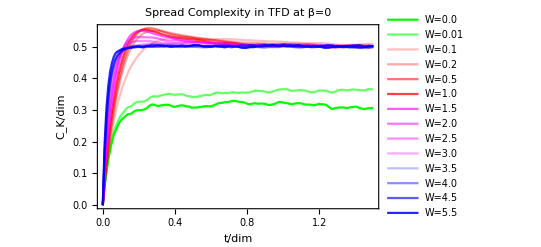

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

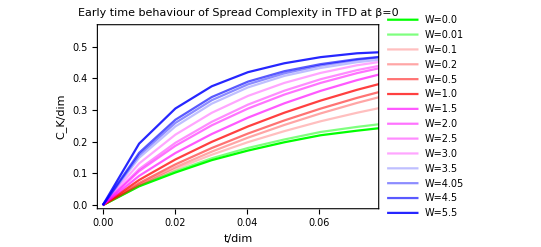

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.5],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.075},Automatic},PlotLabel->Style["Early time behaviour of Spread Complexity in TFD at β=0",Bold,Black]]
```

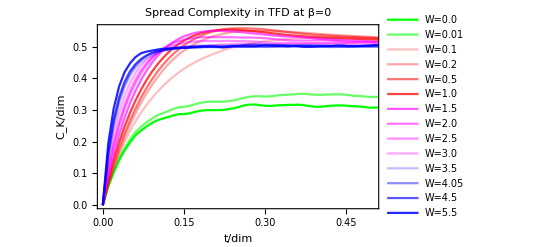

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Italic,Black,16],Style["C_K/dim",Italic,Black,16]},PlotRange->{{0,0.5},Automatic},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

## Full Plots KIPR

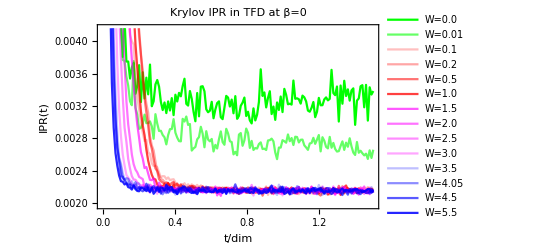

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW0pt1}],Transpose[{tList14,KIPRW0pt2}],Transpose[{tList14,KIPRW0pt5}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW2}],Transpose[{tList14,KIPRW2pt5}],Transpose[{tList14,KIPRW3}],Transpose[{tList14,KIPRW3pt5}],Transpose[{tList14,KIPRW4}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black]]
```

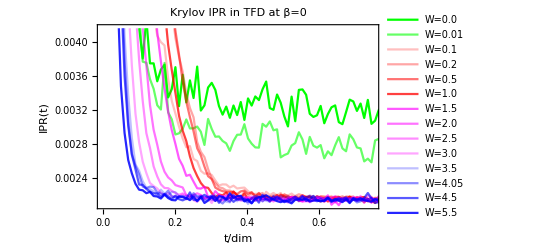

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW0pt1}],Transpose[{tList14,KIPRW0pt2}],Transpose[{tList14,KIPRW0pt5}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW2}],Transpose[{tList14,KIPRW2pt5}],Transpose[{tList14,KIPRW3}],Transpose[{tList14,KIPRW3pt5}],Transpose[{tList14,KIPRW4}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]},PlotRange->Automatic],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.75},Full}]
```

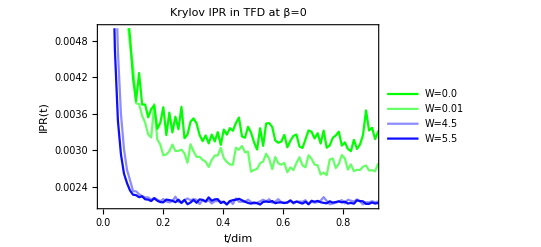

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

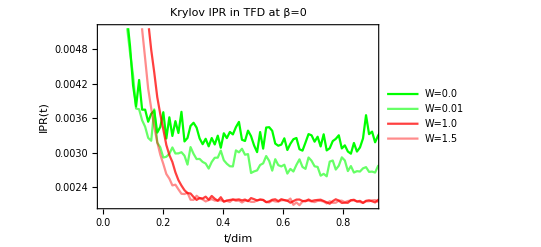

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}]},PlotLegends->{"W=0.0","W=0.01","W=1.0","W=1.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

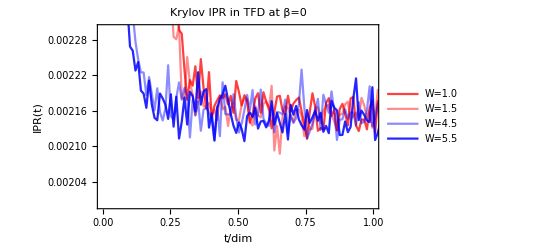

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=1.0","W=1.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,1.0},{0.002,0.00230}}]
```

## Full Plots Entropic Complexity

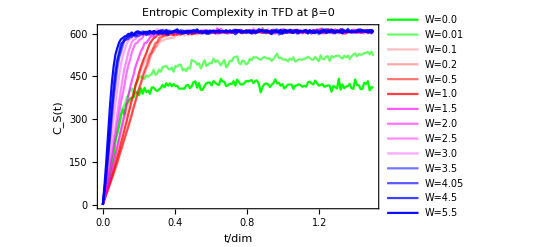

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

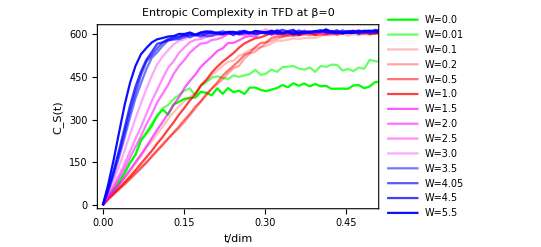

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.5},Full}]
```

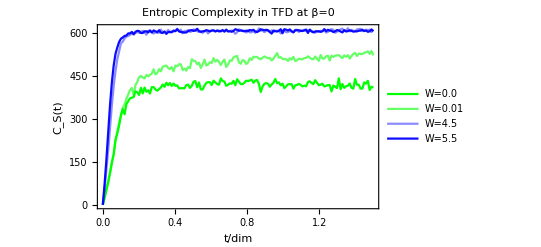

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

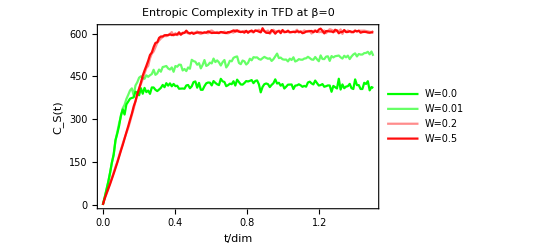

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.2","W=0.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.45],RGBColor[1,0,0,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

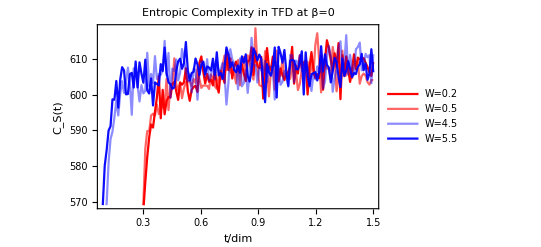

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.2","W=0.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,1],RGBColor[1,0,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

## Peak vs. W

```mathematica
peakList = {Max[KCW0pt1]-KCW0pt1[[-1]],Max[KCW0pt2]-KCW0pt2[[-1]],Max[KCW0pt5]-KCW0pt5[[-1]],Max[KCW1]-KCW1[[-1]],Max[KCW1pt5]-KCW1pt5[[-1]],Max[KCW2]-KCW2[[-1]],Max[KCW2pt5]-KCW2pt5[[-1]],Max[KCW3]-KCW3[[-1]],Max[KCW3pt5]-KCW3pt5[[-1]],Max[KCW4]-KCW4[[-1]],Max[KCW4pt5]-KCW4pt5[[-1]],Max[KCW5pt5]-KCW5pt5[[-1]]};
wList = {0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

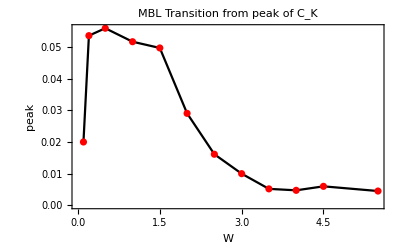

```mathematica
peakWL12=Show[ListLinePlot[Transpose[{wList,peakList}],PlotStyle->Black],ListPlot[Transpose[{wList,peakList}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["peak",Italic,Black,14]},PlotLabel->Style["MBL Transition from peak of C_K",Bold,Black,16]]
```

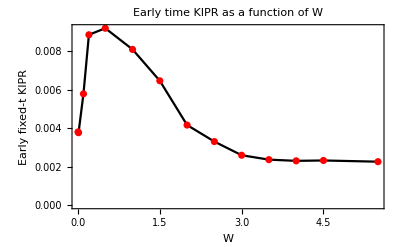

```mathematica
KIPRWFixedtL12 = {KIPRW0[[12]],KIPRW0pt01[[12]],KIPRW0pt1[[12]],KIPRW0pt2[[12]],KIPRW0pt5[[12]],KIPRW1[[12]],KIPRW1pt5[[12]],KIPRW2[[12]],KIPRW2pt5[[12]],KIPRW3[[12]],KIPRW3pt5[[12]],KIPRW4[[12]],KIPRW4pt5[[12]],KIPRW5pt5[[12]]};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWFixedtL12}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWFixedtL12}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Early fixed-t KIPR",Italic,Black,14]},PlotLabel->Style["Early time KIPR as a function of W",Bold,Black,16]]
```

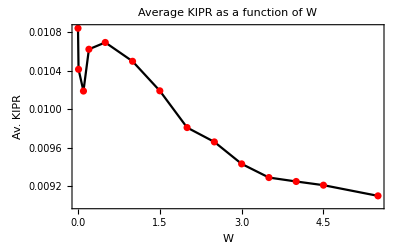

```mathematica
KIPRWavL12 = {KIPRW0//Mean,KIPRW0pt01//Mean,KIPRW0pt1//Mean,KIPRW0pt2//Mean,KIPRW0pt5//Mean,KIPRW1//Mean,KIPRW1pt5//Mean,KIPRW2//Mean,KIPRW2pt5//Mean,KIPRW3//Mean,KIPRW3pt5//Mean,KIPRW4//Mean,KIPRW4pt5//Mean,KIPRW5pt5//Mean};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWavL12}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWavL12}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Av. KIPR",Italic,Black,14]},PlotLabel->Style["Average KIPR as a function of W",Bold,Black,16]]
```

## Plotting L=10 TFD Spread Complexity

```mathematica
tList1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_0_R_100_pbc.txt","Table"]//Flatten;
KCW0L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_0_R_100_pbc.txt","Table"]//Flatten;
KIPRW0L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_0_R_100_pbc.txt","Table"]//Flatten;
KEntW0L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_0_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW0L10 = Exp[#] &/@ KEntW0L10;
```

```mathematica
tList2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_0.01_R_100_pbc.txt","Table"]//Flatten;
KCW0pt01L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_0.01_R_100_pbc.txt","Table"]//Flatten;
KIPRW0pt01L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_0.01_R_100_pbc.txt","Table"]//Flatten;
KEntW0pt01L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_0.01_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW0pt01L10 = Exp[#] &/@ KEntW0pt01L10;
```

```mathematica
KCpltW0pt01=ListLinePlot[Transpose[{tList1,KCW0pt01}],PlotRange->All];
```

```mathematica
tList3L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_0.1_R_100_pbc.txt","Table"]//Flatten;
KCW0pt1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_0.1_R_100_pbc.txt","Table"]//Flatten;
KIPRW0pt1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_0.1_R_100_pbc.txt","Table"]//Flatten;
KEntW0pt1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_0.1_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW0pt1L10 = Exp[#] &/@ KEntW0pt1L10;
```

```mathematica
KCpltW0pt1=ListLinePlot[Transpose[{tList3,KCW0pt1}],PlotRange->All];
```

```mathematica
tList4L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_0.2_R_100_pbc.txt","Table"]//Flatten;
KCW0pt2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_0.2_R_100_pbc.txt","Table"]//Flatten;
KIPRW0pt2L10= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_0.2_R_100_pbc.txt","Table"]//Flatten;
KEntW0pt2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_0.2_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW0pt2L10 = Exp[#] &/@ KEntW0pt2L10;
```

```mathematica
KCpltW0pt2=ListLinePlot[Transpose[{tList4,KCW0pt2}],PlotRange->All];
```

```mathematica
tList5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_0.5_R_100_pbc.txt","Table"]//Flatten;
KCW0pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_0.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW0pt5L10= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_0.5_R_100_pbc.txt","Table"]//Flatten;
KEntW0pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_0.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW0pt5L10 = Exp[#] &/@ KEntW0pt5L10;
```

```mathematica
KCpltW0pt5=ListLinePlot[Transpose[{tList4,KCW0pt5}],PlotRange->All];
```

```mathematica
tList6L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_1_R_100_pbc.txt","Table"]//Flatten;
KCW1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_1_R_100_pbc.txt","Table"]//Flatten;
KIPRW1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_1_R_100_pbc.txt","Table"]//Flatten;
KEntW1L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_1_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW1L10 = Exp[#] &/@ KEntW1L10;
```

```mathematica
KCpltW1=ListLinePlot[Transpose[{tList5,KCW1}],PlotRange->All];
```

```mathematica
tList7L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_1.5_R_100_pbc.txt","Table"]//Flatten;
KCW1pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_1.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW1pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_1.5_R_100_pbc.txt","Table"]//Flatten;
KEntW1pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_1.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW1pt5L10 = Exp[#] &/@ KEntW1pt5L10;
```

```mathematica
KCpltW1pt5=ListLinePlot[Transpose[{tList6,KCW1pt5}],PlotRange->All];
```

```mathematica
tList8L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_2.0_R_100_pbc.txt","Table"]//Flatten;
KCW2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_2.0_R_100_pbc.txt","Table"]//Flatten;
KIPRW2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_2.0_R_100_pbc.txt","Table"]//Flatten;
KEntW2L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_2.0_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW2L10 = Exp[#] &/@ KEntW2L10;
```

```mathematica
KCpltW2=ListLinePlot[Transpose[{tList8,KCW2}],PlotRange->All];
```

```mathematica
tList9L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_2.5_R_100_pbc.txt","Table"]//Flatten;
KCW2pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_2.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW2pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_2.5_R_100_pbc.txt","Table"]//Flatten;
KEntW2pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_2.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW2pt5L10 = Exp[#] &/@ KEntW2pt5L10;
```

```mathematica
KCpltW2pt5=ListLinePlot[Transpose[{tList9,KCW2pt5}],PlotRange->All];
```

```mathematica
tList10L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_3.0_R_100_pbc.txt","Table"]//Flatten;
KCW3L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_3.0_R_100_pbc.txt","Table"]//Flatten;
KIPRW3L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_3.0_R_100_pbc.txt","Table"]//Flatten;
KEntW3L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_3.0_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW3L10 = Exp[#] &/@ KEntW3L10;
```

```mathematica
KCpltW3=ListLinePlot[Transpose[{tList10,KCW3}],PlotRange->All];
```

```mathematica
tList11L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_3.5_R_100_pbc.txt","Table"]//Flatten;
KCW3pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_3.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW3pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_3.5_R_100_pbc.txt","Table"]//Flatten;
KEntW3pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_3.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW3pt5L10 = Exp[#] &/@ KEntW3pt5L10;
```

```mathematica
KCpltW3pt5=ListLinePlot[Transpose[{tList11,KCW3pt5}],PlotRange->All];
```

```mathematica
tList12L10= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_4.0_R_100_pbc.txt","Table"]//Flatten;
KCW4L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_4.0_R_100_pbc.txt","Table"]//Flatten;
KIPRW4L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_4.0_R_100_pbc.txt","Table"]//Flatten;
KEntW4L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_4.0_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW4L10 = Exp[#] &/@ KEntW4L10;
```

```mathematica
KCpltW4=ListLinePlot[Transpose[{tList12,KCW4}],PlotRange->All];
```

```mathematica
tList13L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_4.5_R_100_pbc.txt","Table"]//Flatten;
KCW4pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_4.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW4pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_4.5_R_100_pbc.txt","Table"]//Flatten;
KEntW4pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_4.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW4pt5L10 = Exp[#] &/@ KEntW4pt5L10;
```

```mathematica
KCpltW4pt5=ListLinePlot[Transpose[{tList13,KCW4pt5}],PlotRange->All];
```

```mathematica
tList14L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/t_list_Delta_1_L_10_w_5.5_R_100_pbc.txt","Table"]//Flatten;
KCW5pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/complexity_Delta_1_L_10_w_5.5_R_100_pbc.txt","Table"]//Flatten;
KIPRW5pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_IPR_Delta_1_L_10_w_5.5_R_100_pbc.txt","Table"]//Flatten;
KEntW5pt5L10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L10/krylov_entropy_Delta_1_L_10_w_5.5_R_100_pbc.txt","Table"]//Flatten;
EntComplexityW5pt5L10 = Exp[#] &/@ KEntW5pt5L10;
```

```mathematica
KCpltW5pt5=ListLinePlot[Transpose[{tList14,KCW5pt5}],PlotRange->All];
```

## Full Plots Krylov Spread Complexity

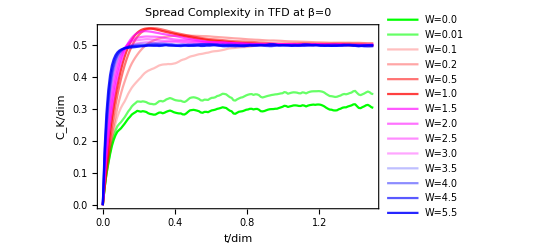

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KCW0L10}],Transpose[{tList14L10,KCW0pt01L10}],Transpose[{tList14L10,KCW0pt1L10}],Transpose[{tList14L10,KCW0pt2L10}],Transpose[{tList14L10,KCW0pt5L10}],Transpose[{tList14L10,KCW1L10}],Transpose[{tList14L10,KCW1pt5L10}],Transpose[{tList14L10,KCW2L10}],Transpose[{tList14L10,KCW2pt5L10}],Transpose[{tList14L10,KCW3L10}],Transpose[{tList14L10,KCW3pt5L10}],Transpose[{tList14L10,KCW4L10}],Transpose[{tList14L10,KCW4pt5L10}],Transpose[{tList14L10,KCW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

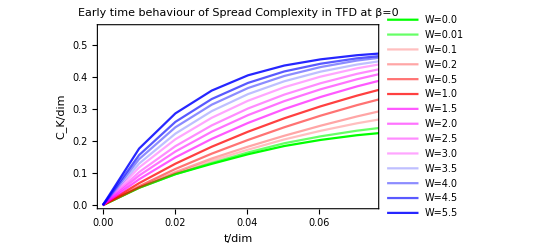

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KCW0L10}],Transpose[{tList14L10,KCW0pt01L10}],Transpose[{tList14L10,KCW0pt1L10}],Transpose[{tList14L10,KCW0pt2L10}],Transpose[{tList14L10,KCW0pt5L10}],Transpose[{tList14L10,KCW1L10}],Transpose[{tList14L10,KCW1pt5L10}],Transpose[{tList14L10,KCW2L10}],Transpose[{tList14L10,KCW2pt5L10}],Transpose[{tList14L10,KCW3L10}],Transpose[{tList14L10,KCW3pt5L10}],Transpose[{tList14L10,KCW4L10}],Transpose[{tList14L10,KCW4pt5L10}],Transpose[{tList14L10,KCW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.075},Automatic},PlotLabel->Style["Early time behaviour of Spread Complexity in TFD at β=0",Bold,Black]]
```

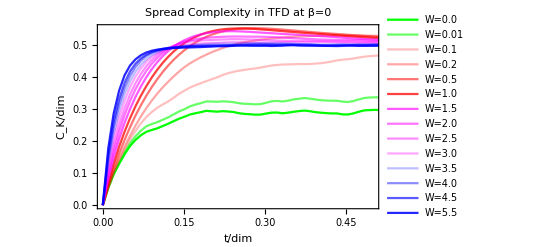

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KCW0L10}],Transpose[{tList14L10,KCW0pt01L10}],Transpose[{tList14L10,KCW0pt1L10}],Transpose[{tList14L10,KCW0pt2L10}],Transpose[{tList14L10,KCW0pt5L10}],Transpose[{tList14L10,KCW1L10}],Transpose[{tList14L10,KCW1pt5L10}],Transpose[{tList14L10,KCW2L10}],Transpose[{tList14L10,KCW2pt5L10}],Transpose[{tList14L10,KCW3L10}],Transpose[{tList14L10,KCW3pt5L10}],Transpose[{tList14L10,KCW4L10}],Transpose[{tList14L10,KCW4pt5L10}],Transpose[{tList14L10,KCW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.5},Automatic},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

## Full Plots KIPR

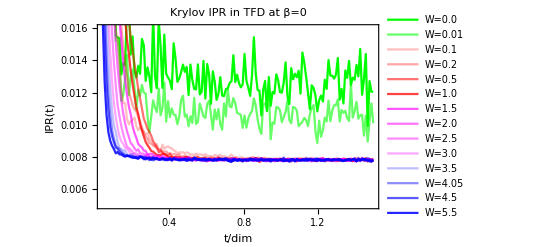

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KIPRW0L10}],Transpose[{tList14L10,KIPRW0pt01L10}],Transpose[{tList14L10,KIPRW0pt1L10}],Transpose[{tList14L10,KIPRW0pt2L10}],Transpose[{tList14L10,KIPRW0pt5L10}],Transpose[{tList14L10,KIPRW1L10}],Transpose[{tList14L10,KIPRW1pt5L10}],Transpose[{tList14L10,KIPRW2L10}],Transpose[{tList14L10,KIPRW2pt5L10}],Transpose[{tList14L10,KIPRW3L10}],Transpose[{tList14L10,KIPRW3pt5L10}],Transpose[{tList14L10,KIPRW4L10}],Transpose[{tList14L10,KIPRW4pt5L10}],Transpose[{tList14L10,KIPRW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{Full,{0.005,0.016}}]
```

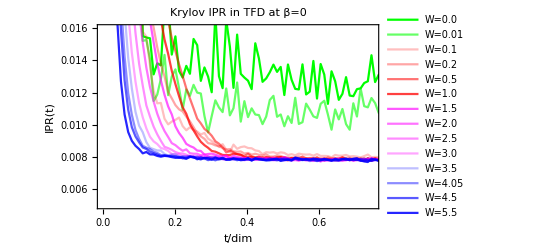

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KIPRW0L10}],Transpose[{tList14L10,KIPRW0pt01L10}],Transpose[{tList14L10,KIPRW0pt1L10}],Transpose[{tList14L10,KIPRW0pt2L10}],Transpose[{tList14L10,KIPRW0pt5L10}],Transpose[{tList14L10,KIPRW1L10}],Transpose[{tList14L10,KIPRW1pt5L10}],Transpose[{tList14L10,KIPRW2L10}],Transpose[{tList14L10,KIPRW2pt5L10}],Transpose[{tList14L10,KIPRW3L10}],Transpose[{tList14L10,KIPRW3pt5L10}],Transpose[{tList14L10,KIPRW4L10}],Transpose[{tList14L10,KIPRW4pt5L10}],Transpose[{tList14L10,KIPRW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.75},{0.005,0.016}}]
```

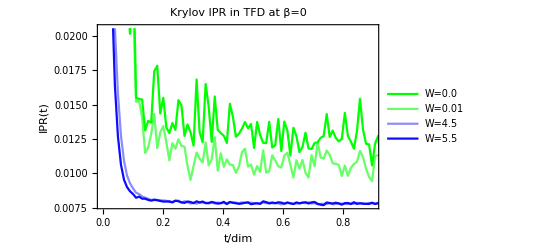

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KIPRW0L10}],Transpose[{tList14L10,KIPRW0pt01L10}],Transpose[{tList14L10,KIPRW4pt5L10}],Transpose[{tList14L10,KIPRW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

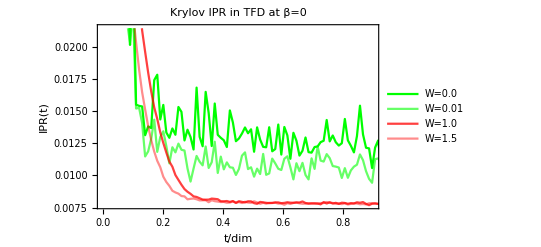

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KIPRW0L10}],Transpose[{tList14L10,KIPRW0pt01L10}],Transpose[{tList14L10,KIPRW1L10}],Transpose[{tList14L10,KIPRW1pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=1.0","W=1.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

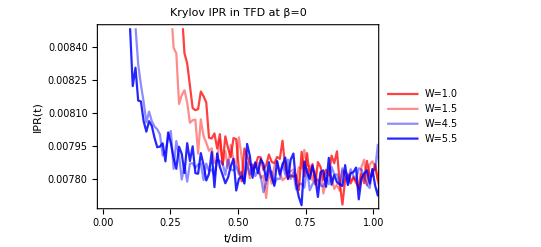

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,KIPRW1L10}],Transpose[{tList14L10,KIPRW1pt5L10}],Transpose[{tList14L10,KIPRW4pt5L10}],Transpose[{tList14L10,KIPRW5pt5L10}]},PlotLegends->{"W=1.0","W=1.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,1.0},Automatic}]
```

## Full Plots Entropic Complexity

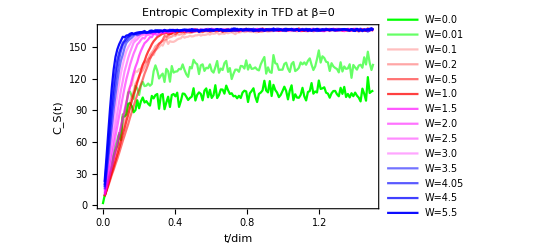

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,EntComplexityW0L10}],Transpose[{tList14L10,EntComplexityW0pt01L10}],Transpose[{tList14L10,EntComplexityW0pt1L10}],Transpose[{tList14L10,EntComplexityW0pt2L10}],Transpose[{tList14L10,EntComplexityW0pt5L10}],Transpose[{tList14L10,EntComplexityW1L10}],Transpose[{tList14L10,EntComplexityW1pt5L10}],Transpose[{tList14L10,EntComplexityW2L10}],Transpose[{tList14L10,EntComplexityW2pt5L10}],Transpose[{tList14L10,EntComplexityW3L10}],Transpose[{tList14L10,EntComplexityW3pt5L10}],Transpose[{tList14L10,EntComplexityW4L10}],Transpose[{tList14L10,EntComplexityW4pt5L10}],Transpose[{tList14L10,EntComplexityW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

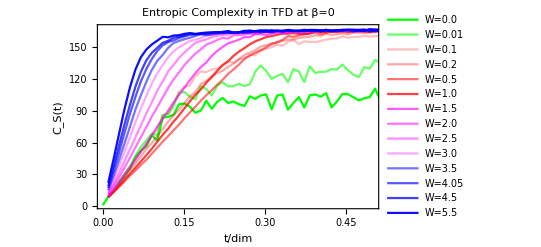

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,EntComplexityW0L10}],Transpose[{tList14L10,EntComplexityW0pt01L10}],Transpose[{tList14L10,EntComplexityW0pt1L10}],Transpose[{tList14L10,EntComplexityW0pt2L10}],Transpose[{tList14L10,EntComplexityW0pt5L10}],Transpose[{tList14L10,EntComplexityW1L10}],Transpose[{tList14L10,EntComplexityW1pt5L10}],Transpose[{tList14L10,EntComplexityW2L10}],Transpose[{tList14L10,EntComplexityW2pt5L10}],Transpose[{tList14L10,EntComplexityW3L10}],Transpose[{tList14L10,EntComplexityW3pt5L10}],Transpose[{tList14L10,EntComplexityW4L10}],Transpose[{tList14L10,EntComplexityW4pt5L10}],Transpose[{tList14L10,EntComplexityW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.5},Full}]
```

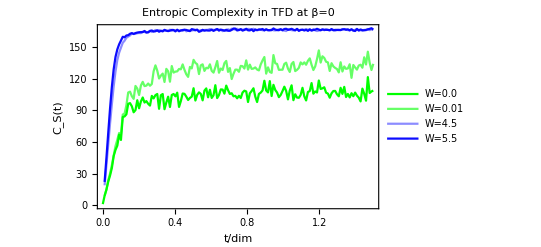

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,EntComplexityW0L10}],Transpose[{tList14L10,EntComplexityW0pt01L10}],Transpose[{tList14L10,EntComplexityW4pt5L10}],Transpose[{tList14L10,EntComplexityW5pt5L10}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

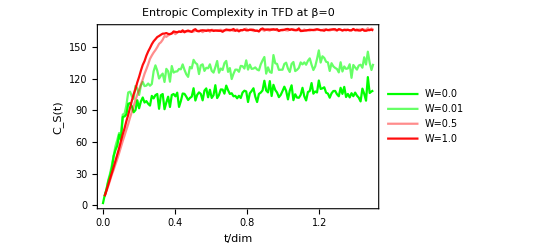

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,EntComplexityW0L10}],Transpose[{tList14L10,EntComplexityW0pt01L10}],Transpose[{tList14L10,EntComplexityW0pt5L10}],Transpose[{tList14L10,EntComplexityW1L10}]},PlotLegends->{"W=0.0","W=0.01","W=0.5","W=1.0"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.45],RGBColor[1,0,0,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

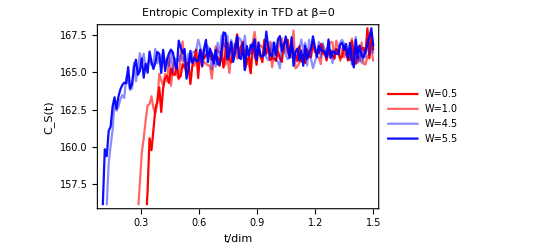

```mathematica
Show[ListLinePlot[{Transpose[{tList14L10,EntComplexityW0pt5L10}],Transpose[{tList14L10,EntComplexityW1L10}],Transpose[{tList14L10,EntComplexityW4pt5L10}],Transpose[{tList14L10,EntComplexityW5pt5L10}]},PlotLegends->{"W=0.5","W=1.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,1],RGBColor[1,0,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

## Peak vs. W

```mathematica
peakList = {Max[KCW0pt1L10]-KCW0pt1L10[[-1]],Max[KCW0pt2L10]-KCW0pt2L10[[-1]],Max[KCW0pt5L10]-KCW0pt5L10[[-1]],Max[KCW1L10]-KCW1L10[[-1]],Max[KCW1pt5L10]-KCW1pt5L10[[-1]],Max[KCW2L10]-KCW2L10[[-1]],Max[KCW2pt5L10]-KCW2pt5L10[[-1]],Max[KCW3L10]-KCW3L10[[-1]],Max[KCW3pt5L10]-KCW3pt5L10[[-1]],Max[KCW4L10]-KCW4L10[[-1]],Max[KCW4pt5L10]-KCW4pt5L10[[-1]],Max[KCW5pt5L10]-KCW5pt5L10[[-1]]};
wList = {0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

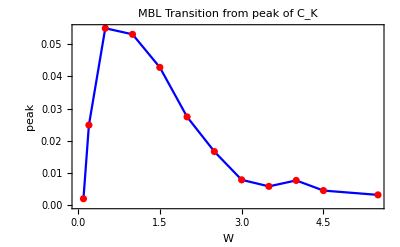

```mathematica
peakWL10=Show[ListLinePlot[Transpose[{wList,peakList}],PlotStyle->Blue],ListPlot[Transpose[{wList,peakList}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["peak",Italic,Black,14]},PlotLabel->Style["MBL Transition from peak of C_K",Bold,Black,16]]
```

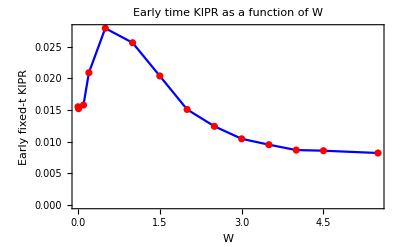

```mathematica
KIPRWFixedtL10 = {KIPRW0L10[[12]],KIPRW0pt01L10[[12]],KIPRW0pt1L10[[12]],KIPRW0pt2L10[[12]],KIPRW0pt5L10[[12]],KIPRW1L10[[12]],KIPRW1pt5L10[[12]],KIPRW2L10[[12]],KIPRW2pt5L10[[12]],KIPRW3L10[[12]],KIPRW3pt5L10[[12]],KIPRW4L10[[12]],KIPRW4pt5L10[[12]],KIPRW5pt5L10[[12]]};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWFixedtL10}],PlotStyle->Blue],ListPlot[Transpose[{wList2,KIPRWFixedtL10}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Early fixed-t KIPR",Italic,Black,14]},PlotLabel->Style["Early time KIPR as a function of W",Bold,Black,16]]
```

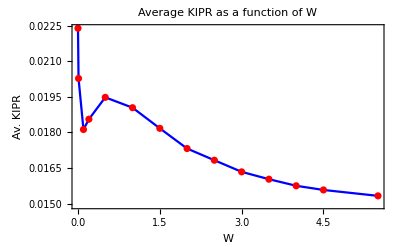

```mathematica
KIPRWavL10 = {KIPRW0L10//Mean,KIPRW0pt01L10//Mean,KIPRW0pt1L10//Mean,KIPRW0pt2L10//Mean,KIPRW0pt5L10//Mean,KIPRW1L10//Mean,KIPRW1pt5L10//Mean,KIPRW2L10//Mean,KIPRW2pt5L10//Mean,KIPRW3L10//Mean,KIPRW3pt5L10//Mean,KIPRW4L10//Mean,KIPRW4pt5L10//Mean,KIPRW5pt5L10//Mean};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWavL10}],PlotStyle->Blue],ListPlot[Transpose[{wList2,KIPRWavL10}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Av. KIPR",Italic,Black,14]},PlotLabel->Style["Average KIPR as a function of W",Bold,Black,16]]
```

## Plotting L=8 TFD Spread Complexity

```mathematica
tList1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_0_R_200_pbc.txt","Table"]//Flatten;
KCW0L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_0_R_200_pbc.txt","Table"]//Flatten;
KIPRW0L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_0_R_200_pbc.txt","Table"]//Flatten;
KEntW0L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_0_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW0L8 = Exp[#] &/@ KEntW0L8;
```

```mathematica
tList2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_0.01_R_200_pbc.txt","Table"]//Flatten;
KCW0pt01L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_0.01_R_200_pbc.txt","Table"]//Flatten;
KIPRW0pt01L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_0.01_R_200_pbc.txt","Table"]//Flatten;
KEntW0pt01L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_0.01_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW0pt01L8 = Exp[#] &/@ KEntW0pt01L8;
```

```mathematica
KCpltW0pt01=ListLinePlot[Transpose[{tList1,KCW0pt01}],PlotRange->All];
```

```mathematica
tList3L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_0.1_R_200_pbc.txt","Table"]//Flatten;
KCW0pt1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_0.1_R_200_pbc.txt","Table"]//Flatten;
KIPRW0pt1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_0.1_R_200_pbc.txt","Table"]//Flatten;
KEntW0pt1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_0.1_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW0pt1L8 = Exp[#] &/@ KEntW0pt1L8;
```

```mathematica
KCpltW0pt1=ListLinePlot[Transpose[{tList3,KCW0pt1}],PlotRange->All];
```

```mathematica
tList4L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_0.2_R_200_pbc.txt","Table"]//Flatten;
KCW0pt2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_0.2_R_200_pbc.txt","Table"]//Flatten;
KIPRW0pt2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_0.2_R_200_pbc.txt","Table"]//Flatten;
KEntW0pt2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_0.2_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW0pt2L8 = Exp[#] &/@ KEntW0pt2L8;
```

```mathematica
KCpltW0pt2=ListLinePlot[Transpose[{tList4,KCW0pt2}],PlotRange->All];
```

```mathematica
tList5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_0.5_R_200_pbc.txt","Table"]//Flatten;
KCW0pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_0.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW0pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_0.5_R_200_pbc.txt","Table"]//Flatten;
KEntW0pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_0.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW0pt5L8 = Exp[#] &/@ KEntW0pt5L8;
```

```mathematica
KCpltW0pt5=ListLinePlot[Transpose[{tList4,KCW0pt5}],PlotRange->All];
```

```mathematica
tList6L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_1_R_200_pbc.txt","Table"]//Flatten;
KCW1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_1_R_200_pbc.txt","Table"]//Flatten;
KIPRW1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_1_R_200_pbc.txt","Table"]//Flatten;
KEntW1L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_1_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW1L8 = Exp[#] &/@ KEntW1L8;
```

```mathematica
KCpltW1=ListLinePlot[Transpose[{tList5,KCW1}],PlotRange->All];
```

```mathematica
tList7L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_1.5_R_200_pbc.txt","Table"]//Flatten;
KCW1pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_1.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW1pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_1.5_R_200_pbc.txt","Table"]//Flatten;
KEntW1pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_1.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW1pt5L8 = Exp[#] &/@ KEntW1pt5L8;
```

```mathematica
KCpltW1pt5=ListLinePlot[Transpose[{tList6,KCW1pt5}],PlotRange->All];
```

```mathematica
tList8L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_2.0_R_200_pbc.txt","Table"]//Flatten;
KCW2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_2.0_R_200_pbc.txt","Table"]//Flatten;
KIPRW2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_2.0_R_200_pbc.txt","Table"]//Flatten;
KEntW2L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_2.0_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW2L8 = Exp[#] &/@ KEntW2L8;
```

```mathematica
KCpltW2=ListLinePlot[Transpose[{tList8,KCW2}],PlotRange->All];
```

```mathematica
tList9L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_2.5_R_200_pbc.txt","Table"]//Flatten;
KCW2pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_2.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW2pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_2.5_R_200_pbc.txt","Table"]//Flatten;
KEntW2pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_2.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW2pt5L8 = Exp[#] &/@ KEntW2pt5L8;
```

```mathematica
KCpltW2pt5=ListLinePlot[Transpose[{tList9,KCW2pt5}],PlotRange->All];
```

```mathematica
tList10L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_3.0_R_200_pbc.txt","Table"]//Flatten;
KCW3L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_3.0_R_200_pbc.txt","Table"]//Flatten;
KIPRW3L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_3.0_R_200_pbc.txt","Table"]//Flatten;
KEntW3L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_3.0_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW3L8 = Exp[#] &/@ KEntW3L8;
```

```mathematica
KCpltW3=ListLinePlot[Transpose[{tList10,KCW3}],PlotRange->All];
```

```mathematica
tList11L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_3.5_R_200_pbc.txt","Table"]//Flatten;
KCW3pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_3.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW3pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_3.5_R_200_pbc.txt","Table"]//Flatten;
KEntW3pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_3.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW3pt5L8 = Exp[#] &/@ KEntW3pt5L8;
```

```mathematica
KCpltW3pt5=ListLinePlot[Transpose[{tList11,KCW3pt5}],PlotRange->All];
```

```mathematica
tList12L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_4.0_R_200_pbc.txt","Table"]//Flatten;
KCW4L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_4.0_R_200_pbc.txt","Table"]//Flatten;
KIPRW4L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_4.0_R_200_pbc.txt","Table"]//Flatten;
KEntW4L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_4.0_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW4L8 = Exp[#] &/@ KEntW4L8;
```

```mathematica
KCpltW4=ListLinePlot[Transpose[{tList12,KCW4}],PlotRange->All];
```

```mathematica
tList13L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_4.5_R_200_pbc.txt","Table"]//Flatten;
KCW4pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_4.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW4pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_4.5_R_200_pbc.txt","Table"]//Flatten;
KEntW4pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_4.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW4pt5L8 = Exp[#] &/@ KEntW4pt5L8;
```

```mathematica
KCpltW4pt5=ListLinePlot[Transpose[{tList13,KCW4pt5}],PlotRange->All];
```

```mathematica
tList14L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/t_list_Delta_1_L_8_w_5.5_R_200_pbc.txt","Table"]//Flatten;
KCW5pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/complexity_Delta_1_L_8_w_5.5_R_200_pbc.txt","Table"]//Flatten;
KIPRW5pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_IPR_Delta_1_L_8_w_5.5_R_200_pbc.txt","Table"]//Flatten;
KEntW5pt5L8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L8/krylov_entropy_Delta_1_L_8_w_5.5_R_200_pbc.txt","Table"]//Flatten;
EntComplexityW5pt5L8 = Exp[#] &/@ KEntW5pt5L8;
```

```mathematica
KCpltW5pt5=ListLinePlot[Transpose[{tList14,KCW5pt5}],PlotRange->All];
```

## Full Plots Krylov Spread Complexity

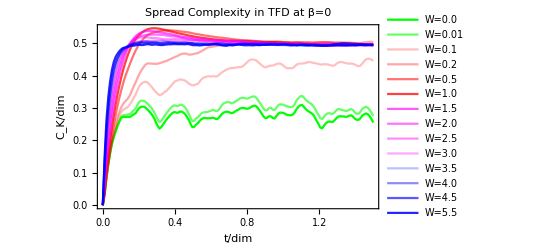

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KCW0L8}],Transpose[{tList14L8,KCW0pt01L8}],Transpose[{tList14L8,KCW0pt1L8}],Transpose[{tList14L8,KCW0pt2L8}],Transpose[{tList14L8,KCW0pt5L8}],Transpose[{tList14L8,KCW1L8}],Transpose[{tList14L8,KCW1pt5L8}],Transpose[{tList14L8,KCW2L8}],Transpose[{tList14L8,KCW2pt5L8}],Transpose[{tList14L8,KCW3L8}],Transpose[{tList14L8,KCW3pt5L8}],Transpose[{tList14L8,KCW4L8}],Transpose[{tList14L8,KCW4pt5L8}],Transpose[{tList14L8,KCW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

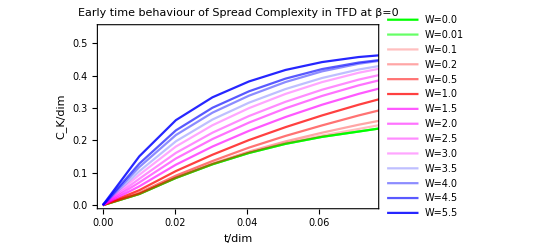

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KCW0L8}],Transpose[{tList14L8,KCW0pt01L8}],Transpose[{tList14L8,KCW0pt1L8}],Transpose[{tList14L8,KCW0pt2L8}],Transpose[{tList14L8,KCW0pt5L8}],Transpose[{tList14L8,KCW1L8}],Transpose[{tList14L8,KCW1pt5L8}],Transpose[{tList14L8,KCW2L8}],Transpose[{tList14L8,KCW2pt5L8}],Transpose[{tList14L8,KCW3L8}],Transpose[{tList14L8,KCW3pt5L8}],Transpose[{tList14L8,KCW4L8}],Transpose[{tList14L8,KCW4pt5L8}],Transpose[{tList14L8,KCW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.075},Automatic},PlotLabel->Style["Early time behaviour of Spread Complexity in TFD at β=0",Bold,Black]]
```

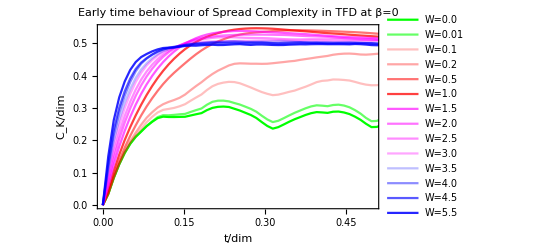

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KCW0L8}],Transpose[{tList14L8,KCW0pt01L8}],Transpose[{tList14L8,KCW0pt1L8}],Transpose[{tList14L8,KCW0pt2L8}],Transpose[{tList14L8,KCW0pt5L8}],Transpose[{tList14L8,KCW1L8}],Transpose[{tList14L8,KCW1pt5L8}],Transpose[{tList14L8,KCW2L8}],Transpose[{tList14L8,KCW2pt5L8}],Transpose[{tList14L8,KCW3L8}],Transpose[{tList14L8,KCW3pt5L8}],Transpose[{tList14L8,KCW4L8}],Transpose[{tList14L8,KCW4pt5L8}],Transpose[{tList14L8,KCW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.5},Automatic},PlotLabel->Style["Early time behaviour of Spread Complexity in TFD at β=0",Bold,Black]]
```

## Full Plots KIPR

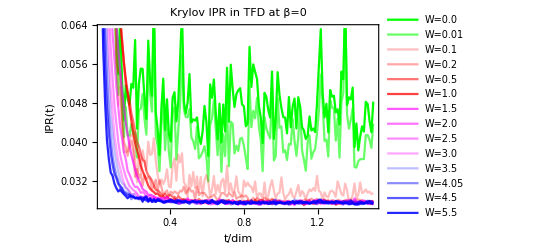

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KIPRW0L8}],Transpose[{tList14L8,KIPRW0pt01L8}],Transpose[{tList14L8,KIPRW0pt1L8}],Transpose[{tList14L8,KIPRW0pt2L8}],Transpose[{tList14L8,KIPRW0pt5L8}],Transpose[{tList14L8,KIPRW1L8}],Transpose[{tList14L8,KIPRW1pt5L8}],Transpose[{tList14L8,KIPRW2L8}],Transpose[{tList14L8,KIPRW2pt5L8}],Transpose[{tList14L8,KIPRW3L8}],Transpose[{tList14L8,KIPRW3pt5L8}],Transpose[{tList14L8,KIPRW4L8}],Transpose[{tList14L8,KIPRW4pt5L8}],Transpose[{tList14L8,KIPRW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

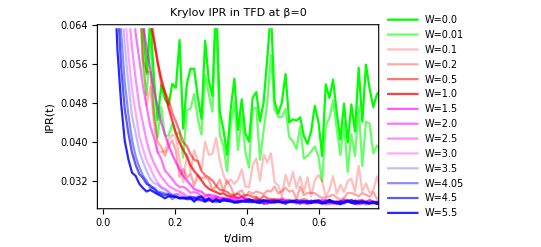

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KIPRW0L8}],Transpose[{tList14L8,KIPRW0pt01L8}],Transpose[{tList14L8,KIPRW0pt1L8}],Transpose[{tList14L8,KIPRW0pt2L8}],Transpose[{tList14L8,KIPRW0pt5L8}],Transpose[{tList14L8,KIPRW1L8}],Transpose[{tList14L8,KIPRW1pt5L8}],Transpose[{tList14L8,KIPRW2L8}],Transpose[{tList14L8,KIPRW2pt5L8}],Transpose[{tList14L8,KIPRW3L8}],Transpose[{tList14L8,KIPRW3pt5L8}],Transpose[{tList14L8,KIPRW4L8}],Transpose[{tList14L8,KIPRW4pt5L8}],Transpose[{tList14L8,KIPRW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.75},Full}]
```

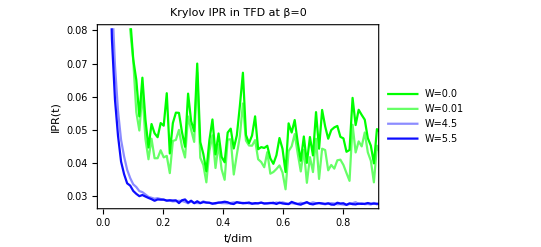

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KIPRW0L8}],Transpose[{tList14L8,KIPRW0pt01L8}],Transpose[{tList14L8,KIPRW4pt5L8}],Transpose[{tList14L8,KIPRW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

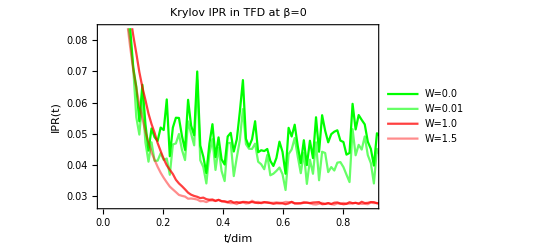

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KIPRW0L8}],Transpose[{tList14L8,KIPRW0pt01L8}],Transpose[{tList14L8,KIPRW1L8}],Transpose[{tList14L8,KIPRW1pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=1.0","W=1.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

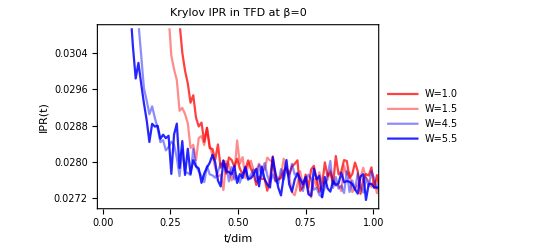

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,KIPRW1L8}],Transpose[{tList14L8,KIPRW1pt5L8}],Transpose[{tList14L8,KIPRW4pt5L8}],Transpose[{tList14L8,KIPRW5pt5L8}]},PlotLegends->{"W=1.0","W=1.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,1.0},Automatic}]
```

## Full Plots Entropic Complexity

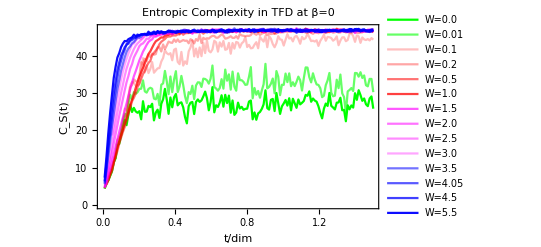

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,EntComplexityW0L8}],Transpose[{tList14L8,EntComplexityW0pt01L8}],Transpose[{tList14L8,EntComplexityW0pt1L8}],Transpose[{tList14L8,EntComplexityW0pt2L8}],Transpose[{tList14L8,EntComplexityW0pt5L8}],Transpose[{tList14L8,EntComplexityW1L8}],Transpose[{tList14L8,EntComplexityW1pt5L8}],Transpose[{tList14L8,EntComplexityW2L8}],Transpose[{tList14L8,EntComplexityW2pt5L8}],Transpose[{tList14L8,EntComplexityW3L8}],Transpose[{tList14L8,EntComplexityW3pt5L8}],Transpose[{tList14L8,EntComplexityW4L8}],Transpose[{tList14L8,EntComplexityW4pt5L8}],Transpose[{tList14L8,EntComplexityW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

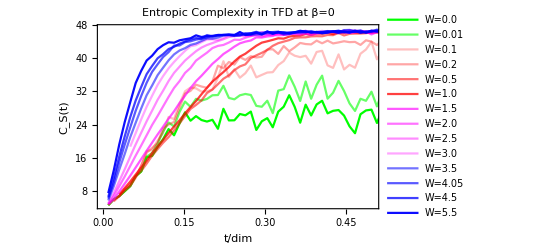

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,EntComplexityW0L8}],Transpose[{tList14L8,EntComplexityW0pt01L8}],Transpose[{tList14L8,EntComplexityW0pt1L8}],Transpose[{tList14L8,EntComplexityW0pt2L8}],Transpose[{tList14L8,EntComplexityW0pt5L8}],Transpose[{tList14L8,EntComplexityW1L8}],Transpose[{tList14L8,EntComplexityW1pt5L8}],Transpose[{tList14L8,EntComplexityW2L8}],Transpose[{tList14L8,EntComplexityW2pt5L8}],Transpose[{tList14L8,EntComplexityW3L8}],Transpose[{tList14L8,EntComplexityW3pt5L8}],Transpose[{tList14L8,EntComplexityW4L8}],Transpose[{tList14L8,EntComplexityW4pt5L8}],Transpose[{tList14L8,EntComplexityW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{{0,0.5},Full}]
```

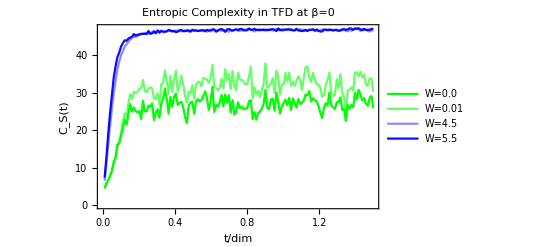

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,EntComplexityW0L8}],Transpose[{tList14L8,EntComplexityW0pt01L8}],Transpose[{tList14L8,EntComplexityW4pt5L8}],Transpose[{tList14L8,EntComplexityW5pt5L8}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

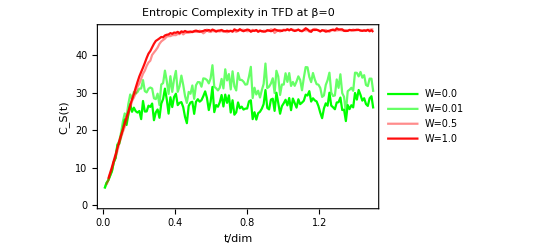

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,EntComplexityW0L8}],Transpose[{tList14L8,EntComplexityW0pt01L8}],Transpose[{tList14L8,EntComplexityW0pt5L8}],Transpose[{tList14L8,EntComplexityW1L8}]},PlotLegends->{"W=0.0","W=0.01","W=0.5","W=1.0"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.45],RGBColor[1,0,0,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

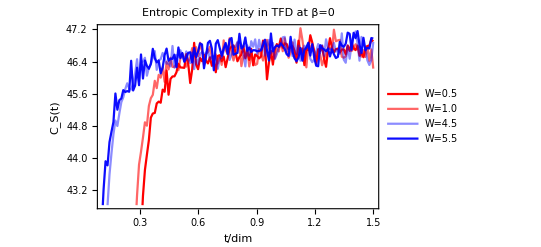

```mathematica
Show[ListLinePlot[{Transpose[{tList14L8,EntComplexityW0pt5L8}],Transpose[{tList14L8,EntComplexityW1L8}],Transpose[{tList14L8,EntComplexityW4pt5L8}],Transpose[{tList14L8,EntComplexityW5pt5L8}]},PlotLegends->{"W=0.5","W=1.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,1],RGBColor[1,0,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

## Peak vs. W

```mathematica
peakList = {Max[KCW0pt1L8]-KCW0pt1L8[[-1]],Max[KCW0pt2L8]-KCW0pt2L8[[-1]],Max[KCW0pt5L8]-KCW0pt5L8[[-1]],Max[KCW1L8]-KCW1L8[[-1]],Max[KCW1pt5L8]-KCW1pt5L8[[-1]],Max[KCW2L8]-KCW2L8[[-1]],Max[KCW2pt5L8]-KCW2pt5L8[[-1]],Max[KCW3L8]-KCW3L8[[-1]],Max[KCW3pt5L8]-KCW3pt5L8[[-1]],Max[KCW4L8]-KCW4L8[[-1]],Max[KCW4pt5L8]-KCW4pt5L8[[-1]],Max[KCW5pt5L8]-KCW5pt5L8[[-1]]};
wList = {0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

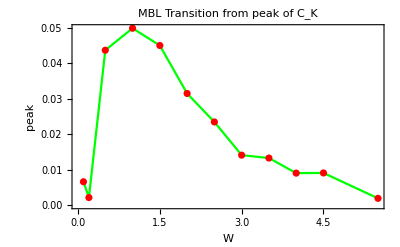

```mathematica
peakWL8=Show[ListLinePlot[Transpose[{wList,peakList}],PlotStyle->Green],ListPlot[Transpose[{wList,peakList}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["peak",Italic,Black,14]},PlotLabel->Style["MBL Transition from peak of C_K",Bold,Black,16]]
```

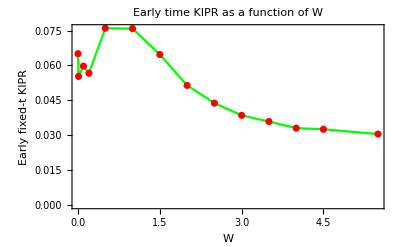

```mathematica
KIPRWFixedtL8 = {KIPRW0L8[[12]],KIPRW0pt01L8[[12]],KIPRW0pt1L8[[12]],KIPRW0pt2L8[[12]],KIPRW0pt5L8[[12]],KIPRW1L8[[12]],KIPRW1pt5L8[[12]],KIPRW2L8[[12]],KIPRW2pt5L8[[12]],KIPRW3L8[[12]],KIPRW3pt5L8[[12]],KIPRW4L8[[12]],KIPRW4pt5L8[[12]],KIPRW5pt5L8[[12]]};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWFixedtL8}],PlotStyle->Green],ListPlot[Transpose[{wList2,KIPRWFixedtL8}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Early fixed-t KIPR",Italic,Black,14]},PlotLabel->Style["Early time KIPR as a function of W",Bold,Black,16]]
```

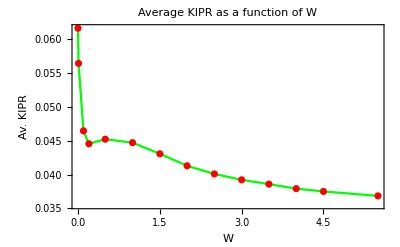

```mathematica
KIPRWavL8 = {KIPRW0L8//Mean,KIPRW0pt01L8//Mean,KIPRW0pt1L8//Mean,KIPRW0pt2L8//Mean,KIPRW0pt5L8//Mean,KIPRW1L8//Mean,KIPRW1pt5L8//Mean,KIPRW2L8//Mean,KIPRW2pt5L8//Mean,KIPRW3L8//Mean,KIPRW3pt5L8//Mean,KIPRW4L8//Mean,KIPRW4pt5L8//Mean,KIPRW5pt5L8//Mean};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWavL8}],PlotStyle->Green],ListPlot[Transpose[{wList2,KIPRWavL8}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Av. KIPR",Italic,Black,14]},PlotLabel->Style["Average KIPR as a function of W",Bold,Black,16]]
```

## Plotting L=14 TFD Spread Complexity

```mathematica
tList1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_0_R_5_pbc.txt","Table"]//Flatten;
KCW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_0_R_5_pbc.txt","Table"]//Flatten;
KIPRW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_0_R_5_pbc.txt","Table"]//Flatten;
KEntW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_0_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW0 = (Exp[#]/3432) &/@ KEntW0;
```

```mathematica
KCpltW0=ListLinePlot[Transpose[{tList1,KCW0}],PlotRange->All];
```

```mathematica
tList2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_0.01_R_5_pbc.txt","Table"]//Flatten;
KCW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_0.01_R_5_pbc.txt","Table"]//Flatten;
KIPRW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_0.01_R_5_pbc.txt","Table"]//Flatten;
KEntW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_0.01_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW0pt01 = (Exp[#]/3432)&/@ KEntW0pt01;
```

```mathematica
KCpltW0pt01=ListLinePlot[Transpose[{tList1,KCW0pt01}],PlotRange->All];
```

```mathematica
tList3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_0.1_R_5_pbc.txt","Table"]//Flatten;
KCW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_0.1_R_5_pbc.txt","Table"]//Flatten;
KIPRW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_0.1_R_5_pbc.txt","Table"]//Flatten;
KEntW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_0.1_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW0pt1 = (Exp[#]/3432)&/@ KEntW0pt1;
```

```mathematica
KCpltW0pt1=ListLinePlot[Transpose[{tList3,KCW0pt1}],PlotRange->All];
```

```mathematica
tList4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_0.2_R_5_pbc.txt","Table"]//Flatten;
KCW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_0.2_R_5_pbc.txt","Table"]//Flatten;
KIPRW0pt2= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_0.2_R_5_pbc.txt","Table"]//Flatten;
KEntW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_0.2_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW0pt2 = (Exp[#]/3432) &/@ KEntW0pt2;
```

```mathematica
KCpltW0pt2=ListLinePlot[Transpose[{tList4,KCW0pt2}],PlotRange->All];
```

```mathematica
tList5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_0.5_R_5_pbc.txt","Table"]//Flatten;
KCW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_0.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_0.5_R_5_pbc.txt","Table"]//Flatten;
KEntW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_0.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW0pt5 = (Exp[#]/3432) &/@ KEntW0pt5;
```

```mathematica
KCpltW0pt5=ListLinePlot[Transpose[{tList4,KCW0pt5}],PlotRange->All];
```

```mathematica
tList6 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_1_R_5_pbc.txt","Table"]//Flatten;
KCW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_1_R_5_pbc.txt","Table"]//Flatten;
KIPRW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_1_R_5_pbc.txt","Table"]//Flatten;
KEntW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_1_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW1 = (Exp[#]/3432)&/@ KEntW1;
```

```mathematica
KCpltW1=ListLinePlot[Transpose[{tList5,KCW1}],PlotRange->All];
```

```mathematica
tList7 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_1.5_R_5_pbc.txt","Table"]//Flatten;
KCW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_1.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_1.5_R_5_pbc.txt","Table"]//Flatten;
KEntW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_1.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW1pt5 = (Exp[#]/3432) &/@ KEntW1pt5;
```

```mathematica
KCpltW1pt5=ListLinePlot[Transpose[{tList6,KCW1pt5}],PlotRange->All];
```

```mathematica
tList8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_2.0_R_5_pbc.txt","Table"]//Flatten;
KCW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_2.0_R_5_pbc.txt","Table"]//Flatten;
KIPRW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_2.0_R_5_pbc.txt","Table"]//Flatten;
KEntW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_2.0_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW2 = (Exp[#]/3432) &/@ KEntW2;
```

```mathematica
KCpltW2=ListLinePlot[Transpose[{tList8,KCW2}],PlotRange->All];
```

```mathematica
tList9 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_2.5_R_5_pbc.txt","Table"]//Flatten;
KCW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_2.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_2.5_R_5_pbc.txt","Table"]//Flatten;
KEntW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_2.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW2pt5 =(Exp[#]/3432) &/@ KEntW2pt5;
```

```mathematica
KCpltW2pt5=ListLinePlot[Transpose[{tList9,KCW2pt5}],PlotRange->All];
```

```mathematica
tList10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_3.0_R_5_pbc.txt","Table"]//Flatten;
KCW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_3.0_R_5_pbc.txt","Table"]//Flatten;
KIPRW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_3.0_R_5_pbc.txt","Table"]//Flatten;
KEntW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_3.0_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW3 =(Exp[#]/3432) &/@ KEntW3;
```

```mathematica
KCpltW3=ListLinePlot[Transpose[{tList10,KCW3}],PlotRange->All];
```

```mathematica
tList11 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_3.5_R_5_pbc.txt","Table"]//Flatten;
KCW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_3.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_3.5_R_5_pbc.txt","Table"]//Flatten;
KEntW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_3.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW3pt5 = (Exp[#]/3432) &/@ KEntW3pt5;
```

```mathematica
KCpltW3pt5=ListLinePlot[Transpose[{tList11,KCW3pt5}],PlotRange->All];
```

```mathematica
tList12 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_4.0_R_5_pbc.txt","Table"]//Flatten;
KCW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_4.0_R_5_pbc.txt","Table"]//Flatten;
KIPRW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_4.0_R_5_pbc.txt","Table"]//Flatten;
KEntW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_4.0_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW4 = (Exp[#]/3432) &/@ KEntW4;
```

```mathematica
KCpltW4=ListLinePlot[Transpose[{tList12,KCW4}],PlotRange->All];
```

```mathematica
tList13 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_4.5_R_5_pbc.txt","Table"]//Flatten;
KCW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_4.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_4.5_R_5_pbc.txt","Table"]//Flatten;
KEntW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_4.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW4pt5 = (Exp[#]/3432) &/@ KEntW4pt5;
```

```mathematica
KCpltW4pt5=ListLinePlot[Transpose[{tList13,KCW4pt5}],PlotRange->All];
```

```mathematica
tList14 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/t_list_Delta_1_L_14_w_5.5_R_5_pbc.txt","Table"]//Flatten;
KCW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/complexity_Delta_1_L_14_w_5.5_R_5_pbc.txt","Table"]//Flatten;
KIPRW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_IPR_Delta_1_L_14_w_5.5_R_5_pbc.txt","Table"]//Flatten;
KEntW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_TFD/L14/krylov_entropy_Delta_1_L_14_w_5.5_R_5_pbc.txt","Table"]//Flatten;
EntComplexityW5pt5 =(Exp[#]/3432) &/@ KEntW5pt5;
```

```mathematica
KCpltW5pt5=ListLinePlot[Transpose[{tList14,KCW5pt5}],PlotRange->All];
```

## Full Plots Krylov Spread Complexity

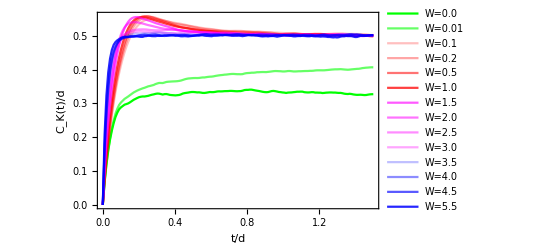

```mathematica
pKCL14=Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/d",Bold,Black,16],Style["C_K(t)/d",Bold,Black,16]},LabelStyle->{Bold,Black,12}]
```

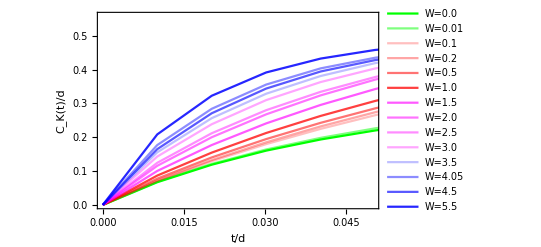

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.5],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/d",Bold,Black,16],Style["C_K(t)/d",Bold,Black,16]},PlotRange->{{0,0.05},Automatic},LabelStyle->{Bold,Black,12}]
```

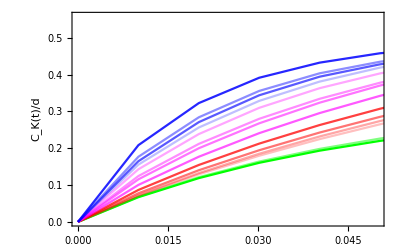

```mathematica
pKCL14b2=Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.5],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["",Bold,Black,8],Style["C_K(t)/d",Bold,Black,8]},PlotRange->{{0,0.05},Automatic},LabelStyle->{Bold,Black,8}]
```

```mathematica
Show[pKCL14,Epilog->Inset[pKCL14b2,{1.05,0.13}]]
```

-Graphics-

```mathematica
Export["KC_TFD_L14_full.pdf",%2265]
```

KC_TFD_L14_full.pdf

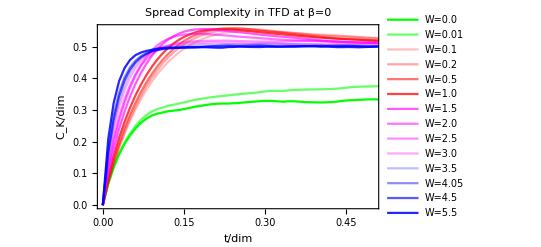

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Italic,Black,16],Style["C_K/dim",Italic,Black,16]},PlotRange->{{0,0.5},Automatic},PlotLabel->Style["Spread Complexity in TFD at β=0",Bold,Black]]
```

## Full Plots KIPR

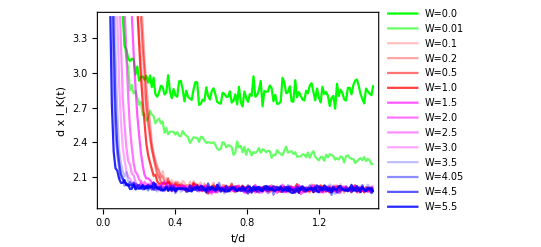

```mathematica
pKIPRL14=Show[ListLinePlot[{Transpose[{tList14,3432 KIPRW0}],Transpose[{tList14,3432 KIPRW0pt01}],Transpose[{tList14,3432 KIPRW0pt1}],Transpose[{tList14,3432 KIPRW0pt2}],Transpose[{tList14,3432 KIPRW0pt5}],Transpose[{tList14,3432 KIPRW1}],Transpose[{tList14,3432 KIPRW1pt5}],Transpose[{tList14,3432 KIPRW2}],Transpose[{tList14,3432 KIPRW2pt5}],Transpose[{tList14,3432 KIPRW3}],Transpose[{tList14,3432 KIPRW3pt5}],Transpose[{tList14,3432 KIPRW4}],Transpose[{tList14,3432 KIPRW4pt5}],Transpose[{tList14,3432 KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/d",Bold,Black,16],Style["d x I_K(t)",Black,16,"TeX"]},LabelStyle->{Bold,Black,12}]
```

```mathematica
Export["KIPR_L14_FULL.pdf",pKIPRL14]
```

KIPR_L14_FULL.pdf

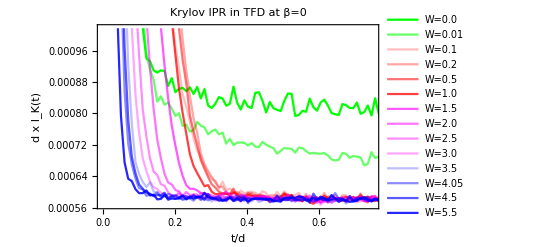

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW0pt1}],Transpose[{tList14,KIPRW0pt2}],Transpose[{tList14,KIPRW0pt5}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW2}],Transpose[{tList14,KIPRW2pt5}],Transpose[{tList14,KIPRW3}],Transpose[{tList14,KIPRW3pt5}],Transpose[{tList14,KIPRW4}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]},PlotRange->Automatic],Frame->True,FrameLabel->{Style["t/d",Bold,Black,16],Style["d x I_K(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.75},Full}]
```

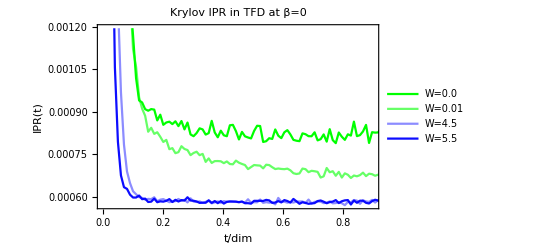

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

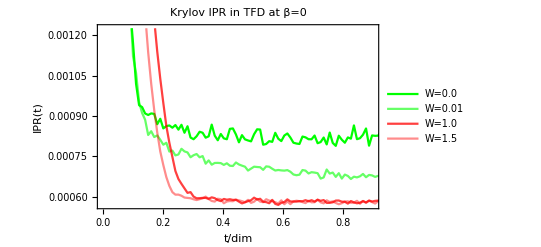

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}]},PlotLegends->{"W=0.0","W=0.01","W=1.0","W=1.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

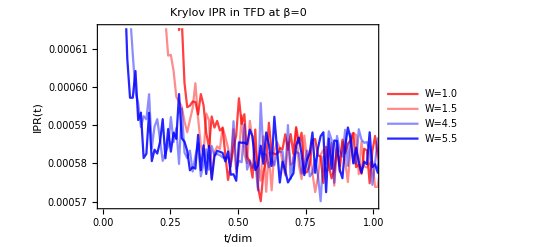

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=1.0","W=1.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,1.0},Automatic}]
```

## Full Plots Entropic Complexity

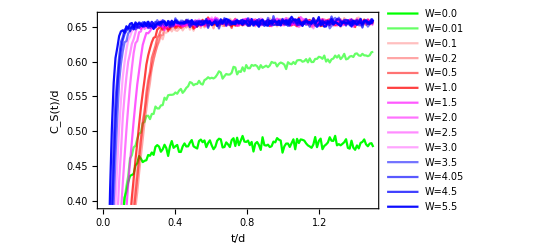

```mathematica
pKECL14=Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/d",Bold,Black,16],Style["C_S(t)/d",Bold,Black,16]},LabelStyle->Directive[Bold, Black,12]]
```

```mathematica
Export["KEC_L14_FULL.pdf",pKECL14]
```

KEC_L14_FULL.pdf

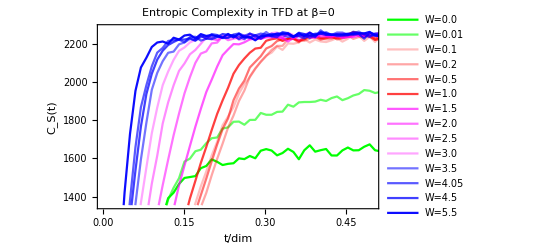

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.5},Full}]
```

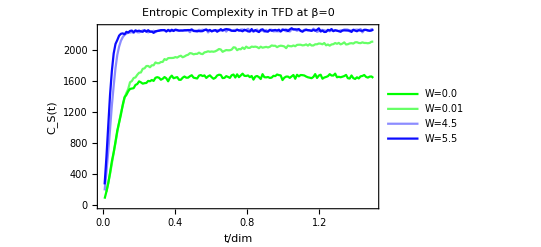

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

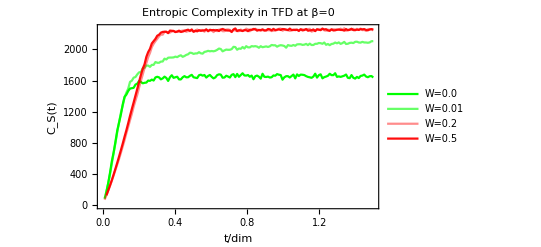

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.2","W=0.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.45],RGBColor[1,0,0,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

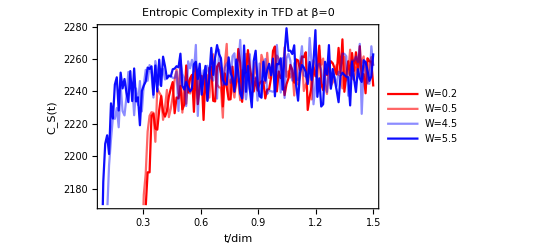

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.2","W=0.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,1],RGBColor[1,0,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

## Peak vs. W

```mathematica
peakList = {Max[KCW0pt1]-KCW0pt1[[-1]],Max[KCW0pt2]-KCW0pt2[[-1]],Max[KCW0pt5]-KCW0pt5[[-1]],Max[KCW1]-KCW1[[-1]],Max[KCW1pt5]-KCW1pt5[[-1]],Max[KCW2]-KCW2[[-1]],Max[KCW2pt5]-KCW2pt5[[-1]],Max[KCW3]-KCW3[[-1]],Max[KCW3pt5]-KCW3pt5[[-1]],Max[KCW4]-KCW4[[-1]],Max[KCW4pt5]-KCW4pt5[[-1]],Max[KCW5pt5]-KCW5pt5[[-1]]};
wList = {0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

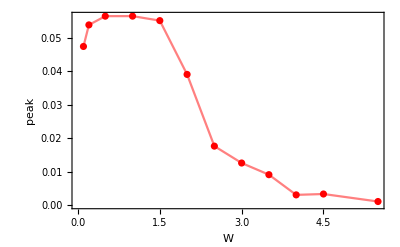

```mathematica
peakWL14=Show[ListLinePlot[Transpose[{wList,peakList}],PlotStyle->Pink],ListPlot[Transpose[{wList,peakList}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,16,Bold],Style["peak",Italic,Black,16,Bold]},PlotLabel->Style["",Bold,Black,16],LabelStyle->Directive[Bold,Black,12]]
```

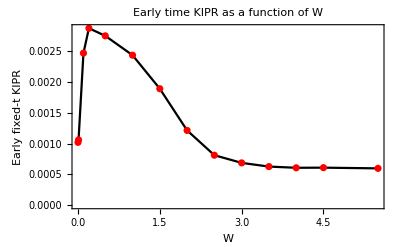

```mathematica
KIPRWFixedtL14 = {KIPRW0[[12]],KIPRW0pt01[[12]],KIPRW0pt1[[12]],KIPRW0pt2[[12]],KIPRW0pt5[[12]],KIPRW1[[12]],KIPRW1pt5[[12]],KIPRW2[[12]],KIPRW2pt5[[12]],KIPRW3[[12]],KIPRW3pt5[[12]],KIPRW4[[12]],KIPRW4pt5[[12]],KIPRW5pt5[[12]]};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWFixedtL14}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWFixedtL14}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Early fixed-t KIPR",Italic,Black,14]},PlotLabel->Style["Early time KIPR as a function of W",Bold,Black,16]]
```

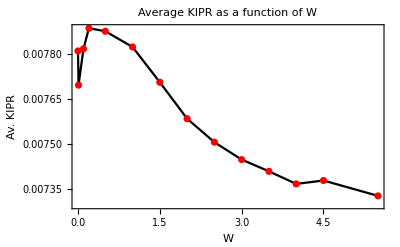

```mathematica
KIPRWavL14 = {KIPRW0//Mean,KIPRW0pt01//Mean,KIPRW0pt1//Mean,KIPRW0pt2//Mean,KIPRW0pt5//Mean,KIPRW1//Mean,KIPRW1pt5//Mean,KIPRW2//Mean,KIPRW2pt5//Mean,KIPRW3//Mean,KIPRW3pt5//Mean,KIPRW4//Mean,KIPRW4pt5//Mean,KIPRW5pt5//Mean};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWavL14}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWavL14}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Av. KIPR",Italic,Black,14]},PlotLabel->Style["Average KIPR as a function of W",Bold,Black,16]]
```

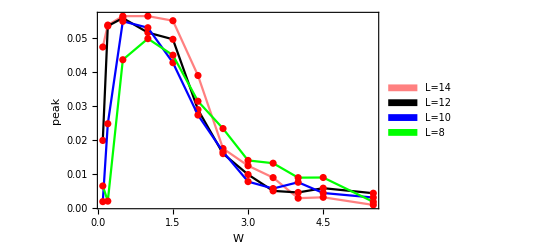

```mathematica
Legended[Show[peakWL14,peakWL12,peakWL10,peakWL8,PlotRange->{Full,Full}],Placed[SwatchLegend[{Pink,Black,Blue,Green},{"L=14","L=12","L=10","L=8"}],{.8,.65}]]
```

```mathematica
SetDirectory["/Users/aneekphys/Documents/MBL1 plots"];
```

```mathematica
Export["peak_vs_W.pdf",%2241];
```